# Constructing protein surfaces

Yury Polyachenko

MIPT

Goal: To create a WL package which enables one to construct and visualize surfaces of proteins.
Results: The package implements the 2 main functions corresponding to the 2 types of surfaces. Tools necessary for sound work with proteins are also provided. More specifically the constructions of solvent accessible surface (SAS1) and of solvent excluded surface (SES1) are implemented using MSMS program3. SAS of a protein is a surface formed by points which a center of a probe solvent molecule rolling over the protein can occupy. SES of a molecule is the inner boundary of the union of all possible probes that do not overlap with the protein. PDB files often do not have hydrogen atoms in them so one may want to protonate a protein before surface analysis to gain a surface closer to the one acting in a real world. Often the impact of protonation on a surface is minimal, but it may not always be the case. A function for protonation is implemented using the Reduce program4.
Methods:

## Wolfram Community Post (material for blog post)

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

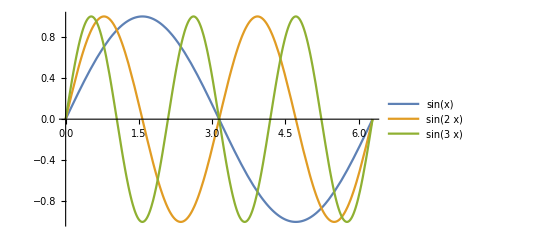

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

## Complete project work

<describe ideas or arguments in a clear narrative format. explain how the topic/idea is studied and how it is implemented in the Wolfram language codes>

<one-line text, explaining the code only> Plot several functions with a legend:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

-Graphics-

## Keywords

<Keyword1>

Keyword2

....

## Acknowledgment

Mentor: <Mentor first name and last name>

<text>

## References

1	Word JM, Lovell SC, Richardson JS, Richardson DC. Asparagine and glutamine: using hydrogen atom contacts in the choice of side-chain amide orientation. J Mol Biol. 1999;285(4):1735-1747. doi:10.1006/jmbi.1998.2401

2	Word JM, Lovell SC, Richardson JS, Richardson DC. Asparagine and glutamine: using hydrogen atom contacts in the choice of side-chain amide orientation. J Mol Biol. 1999;285(4):1735-1747. doi:10.1006/jmbi.1998.2401

3	Word JM, Lovell SC, Richardson JS, Richardson DC. Asparagine and glutamine: using hydrogen atom contacts in the choice of side-chain amide orientation. J Mol Biol. 1999;285(4):1735-1747. doi:10.1006/jmbi.1998.2401

4	Sanner MF, Olson AJ, Spehner JC. Reduced surface: an efficient way to compute molecular surfaces. Biopolymers. 1996;38(3):305-320. doi:10.1002/(SICI)1097-0282(199603)38:3%3C305::AID-BIP4%3E3.0.CO;2-Y